```mathematica
Quit[]
```

## Load Model and Compute Diagrams

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
$FCVerbose=0;
Needs["FeynCalc`"]
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$FAVerbose=0;
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;

(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"LesHouchesModelFreezeIn-leptons_FA/LesHouchesModelFreezeIn-leptons_FA",InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
```

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →3, with {} →{-F[3],F[3],V[1]} and all the momenta set as outgoing ({} → {p1,p2,p3}).
However the choice below produces nicer diagrams.

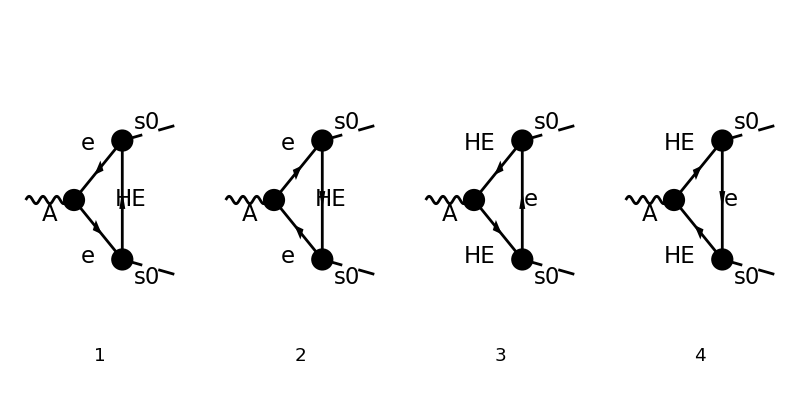

```mathematica
topsCT = CreateCTTopologies[1,1->2];
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies,SelfEnergyCTs}];
processGGT =  {V[1]}->  {S[4],S[4]};
allDiags = InsertFields[Join[tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{F[5],F[6],S[3]}];
goodDiags=DiagramDelete[allDiags,{4}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{4,1},ImageSize->{ 800,400},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

## Compute Amplitude

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{-p3},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,SUNIndexNames->{cc3,aa,bb},SUNFIndexNames->{a,c1,c2},DropSumOver->True,LorentzIndexNames->{ μ}, SMP->True,List->False,Contract->True,ChangeDimension->4,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)];
ampB =FullSimplify[SUNSimplify[DiracSimplify[FCReplaceMomenta[ampA,{p3->-p1-p2}]]]];
```

```mathematica
ampB2=ChangeDimension[DiracSimplify[ampB,DiracTrace->True],D]
```

4 ⅈ EL yHEeR^2 (ϵ^)^μp1p2q (1/((q^2-Me^2).((p1-q)^2-mHE^2).((p1+p2-q)^2-Me^2))-1/((q^2-mHE^2).((p1-q)^2-Me^2).((p1+p2-q)^2-mHE^2)))

Evaluate Loop integrals:

```mathematica
ampC =FCCanonicalizeDummyIndices[( TID[ampB2,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True,PaVeAutoOrder->False]//Simplify),LorentzIndexNames-> {μ,ν}];
```

```mathematica
ampC
```

0

```mathematica
FCClearScalarProducts[];
SPD[p1,p2]=1/2(SPD[p3,p3]-SPD[p1,p1]-SPD[p2,p2]);
ampD=FullSimplify[DiracSimplify[ampC]];
ampEsimp2=Simplify[(ExpandScalarProduct[DiracSimplify[ampD]])//.{B0[a_,b_,c_,___]->PaVe[0,{a},{b,c}],PaVe[1,{a_},{b_,c_},___]->PaVe[1,{a},{b,c},PaVeAutoReduce->False],PaVe[0,{a_},{b_,c_},___]->PaVe[0,{a},{b,c}]}];
```

```mathematica
ampEsimp2
```

0